```mathematica
r[t_, a_,b_]:=Sign[Cos[3(t+π/3)]](Abs[Cos[3(t+π/3)]])^a+b;
```

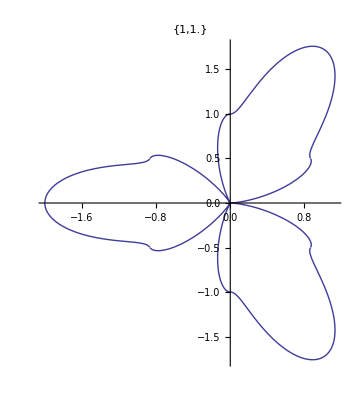
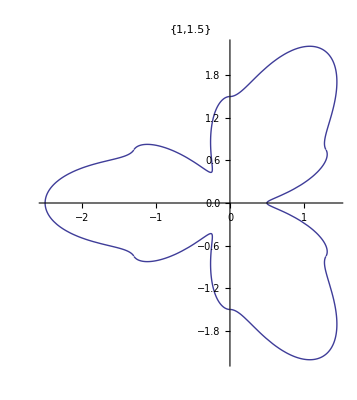
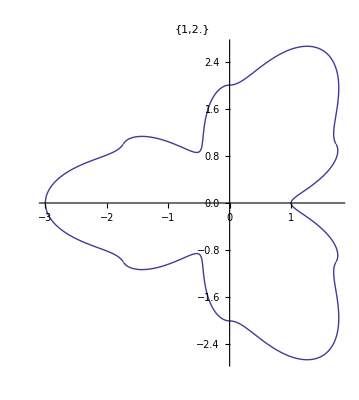
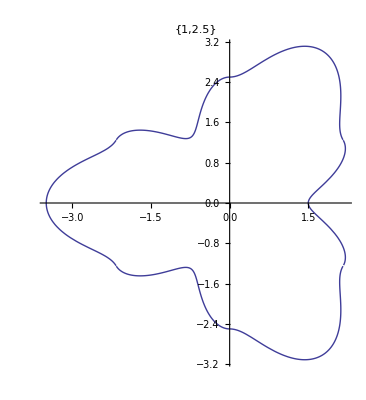
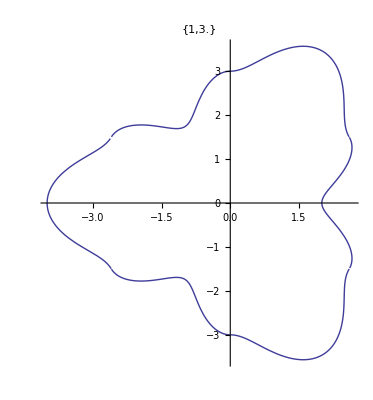
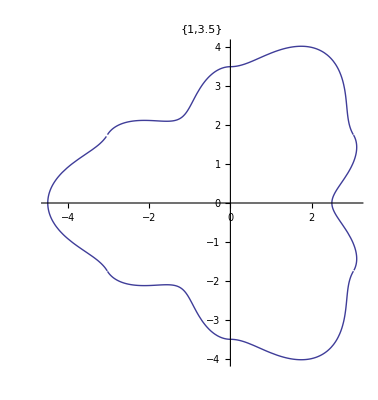
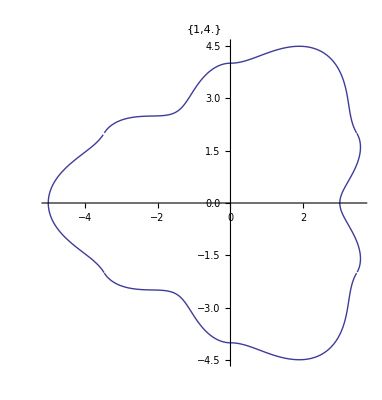
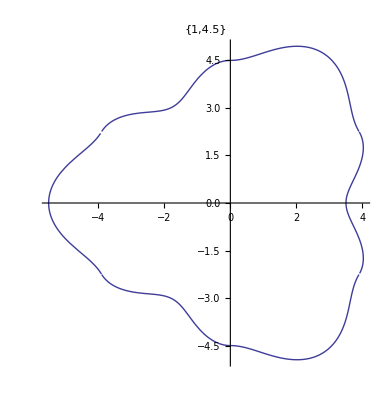

```mathematica
Table[PolarPlot[r[t, 2/a, b],{t,0,2Pi},PlotLabel->{a,b}],{a,6},{b,1,6,0.5}]
```

```mathematica
Table[{N[r[t,1/2,2]Cos[t]],N[r[t,1/2,2]Sin[t]]},{t,0,2 Pi,Pi/36}]
```

{{1.,0.},{1.01331,0.0886535},{1.05315,0.185699},{1.11961,0.299998},{1.21492,0.442196},{1.35154,0.630233},{1.73205,1.},{2.05504,1.43896},{2.07376,1.74009},{2.00882,2.00882},{1.88376,2.24497},{1.71087,2.44338},{1.5,2.59808},{1.26059,2.70335},{1.00233,2.75387},{0.735278,2.7441},{0.470084,2.66598},{0.218651,2.4992},{0.,2.},{-0.129972,1.48558},{-0.224509,1.27325},{-0.299998,1.11961},{-0.365755,1.0049},{-0.429881,0.921882},{-0.5,0.866025},{-0.583433,0.833229},{-0.687394,0.819204},{-0.81961,0.81961},{-0.990414,0.831056},{-1.22157,0.85535},{-1.73205,1.},{-2.27369,1.06024},{-2.54385,0.925885},{-2.7441,0.735278},{-2.88608,0.508894},{-2.97146,0.259969},{-3.,0.},{-2.97146,-0.259969},{-2.88608,-0.508894},{-2.7441,-0.735278},{-2.54385,-0.925885},{-2.27369,-1.06024},{-1.73205,-1.},{-1.22157,-0.85535},{-0.990414,-0.831056},{-0.81961,-0.81961},{-0.687394,-0.819204},{-0.583433,-0.833229},{-0.5,-0.866025},{-0.429881,-0.921882},{-0.365755,-1.0049},{-0.299998,-1.11961},{-0.224509,-1.27325},{-0.129972,-1.48558},{0.,-2.},{0.218651,-2.4992},{0.470084,-2.66598},{0.735278,-2.7441},{1.00233,-2.75387},{1.26059,-2.70335},{1.5,-2.59808},{1.71087,-2.44338},{1.88376,-2.24497},{2.00882,-2.00882},{2.07376,-1.74009},{2.05504,-1.43896},{1.73205,-1.},{1.35154,-0.630233},{1.21492,-0.442196},{1.11961,-0.299998},{1.05315,-0.185699},{1.01331,-0.0886535},{1.,0.}}

```mathematica
Table[{N[r[t,1/2,1.5]Cos[t]],N[r[t,1/2,1.5]Sin[t]]},{t,0,2 Pi,Pi/36}]
```

{{0.5,0.},{0.515217,0.0450756},{0.560745,0.0988744},{0.636645,0.170589},{0.745076,0.271185},{0.898384,0.418923},{1.29904,0.75},{1.64547,1.15217},{1.69074,1.4187},{1.65526,1.65526},{1.56236,1.86195},{1.42408,2.0338},{1.25,2.16506},{1.04928,2.25019},{0.831316,2.28402},{0.605869,2.26113},{0.38326,2.17358},{0.175073,2.0011},{0.,1.5},{-0.0863938,0.987485},{-0.137684,0.780847},{-0.170589,0.636645},{-0.194745,0.535056},{-0.218572,0.468729},{-0.25,0.433013},{-0.296645,0.423653},{-0.366,0.436182},{-0.466057,0.466057},{-0.607391,0.509662},{-0.811991,0.568562},{-1.29904,0.75},{-1.82054,0.848931},{-2.074,0.754875},{-2.26113,0.605869},{-2.39368,0.42207},{-2.47337,0.216392},{-2.5,0.},{-2.47337,-0.216392},{-2.39368,-0.42207},{-2.26113,-0.605869},{-2.074,-0.754875},{-1.82054,-0.848931},{-1.29904,-0.75},{-0.811991,-0.568562},{-0.607391,-0.509662},{-0.466057,-0.466057},{-0.366,-0.436182},{-0.296645,-0.423653},{-0.25,-0.433013},{-0.218572,-0.468729},{-0.194745,-0.535056},{-0.170589,-0.636645},{-0.137684,-0.780847},{-0.0863938,-0.987485},{0.,-1.5},{0.175073,-2.0011},{0.38326,-2.17358},{0.605869,-2.26113},{0.831316,-2.28402},{1.04928,-2.25019},{1.25,-2.16506},{1.42408,-2.0338},{1.56236,-1.86195},{1.65526,-1.65526},{1.69074,-1.4187},{1.64547,-1.15217},{1.29904,-0.75},{0.898384,-0.418923},{0.745076,-0.271185},{0.636645,-0.170589},{0.560745,-0.0988744},{0.515217,-0.0450756},{0.5,0.}}

```mathematica
Table[{N[r[t,1/2,3.5]Cos[t]],N[r[t,1/2,3.5]Sin[t]]},{t,0,2 Pi,Pi/36}]
```

{{2.5,0.},{2.50761,0.219387},{2.53036,0.446171},{2.5685,0.688227},{2.62446,0.955226},{2.711,1.26416},{3.03109,1.75},{3.28377,2.29932},{3.22283,2.70428},{3.06948,3.06948},{2.84794,3.39404},{2.57124,3.67211},{2.25,3.89711},{1.89452,4.06281},{1.51536,4.16341},{1.12351,4.19298},{0.730556,4.14319},{0.349385,3.99349},{0.,3.5},{-0.260705,2.97987},{-0.484981,2.75046},{-0.688227,2.5685},{-0.878785,2.41444},{-1.06381,2.28134},{-1.25,2.16506},{-1.4438,2.06196},{-1.65158,1.96827},{-1.88027,1.88027},{-2.13948,1.79524},{-2.45029,1.71571},{-3.03109,1.75},{-3.63315,1.69417},{-3.95339,1.43892},{-4.19298,1.12351},{-4.36329,0.769366},{-4.46576,0.390703},{-4.5,0.},{-4.46576,-0.390703},{-4.36329,-0.769366},{-4.19298,-1.12351},{-3.95339,-1.43892},{-3.63315,-1.69417},{-3.03109,-1.75},{-2.45029,-1.71571},{-2.13948,-1.79524},{-1.88027,-1.88027},{-1.65158,-1.96827},{-1.4438,-2.06196},{-1.25,-2.16506},{-1.06381,-2.28134},{-0.878785,-2.41444},{-0.688227,-2.5685},{-0.484981,-2.75046},{-0.260705,-2.97987},{0.,-3.5},{0.349385,-3.99349},{0.730556,-4.14319},{1.12351,-4.19298},{1.51536,-4.16341},{1.89452,-4.06281},{2.25,-3.89711},{2.57124,-3.67211},{2.84794,-3.39404},{3.06948,-3.06948},{3.22283,-2.70428},{3.28377,-2.29932},{3.03109,-1.75},{2.711,-1.26416},{2.62446,-0.955226},{2.5685,-0.688227},{2.53036,-0.446171},{2.50761,-0.219387},{2.5,0.}}

```mathematica
rho[a_,b_]:=a+b Sin[8t];
Table[{N[rho[1,1/2]Cos[t]],N[rho[1,1/2]Sin[t]]},{t,0,2 Pi,Pi/36}]
```

{{1.,0.},{1.31637,0.115167},{1.46973,0.259153},{1.38418,0.370891},{1.10039,0.400509},{0.75132,0.350346},{0.491025,0.283494},{0.415798,0.291145},{0.519843,0.4362},{0.707107,0.707107},{0.849376,1.01225},{0.856008,1.22251},{0.716506,1.24103},{0.49489,1.0613},{0.283531,0.778996},{0.146747,0.547668},{0.0881431,0.499885},{0.0591444,0.676024},{0.,1.},{-0.115167,1.31637},{-0.259153,1.46973},{-0.370891,1.38418},{-0.400509,1.10039},{-0.350346,0.75132},{-0.283494,0.491025},{-0.291145,0.415798},{-0.4362,0.519843},{-0.707107,0.707107},{-1.01225,0.849376},{-1.22251,0.856008},{-1.24103,0.716506},{-1.0613,0.49489},{-0.778996,0.283531},{-0.547668,0.146747},{-0.499885,0.0881431},{-0.676024,0.0591444},{-1.,0.},{-1.31637,-0.115167},{-1.46973,-0.259153},{-1.38418,-0.370891},{-1.10039,-0.400509},{-0.75132,-0.350346},{-0.491025,-0.283494},{-0.415798,-0.291145},{-0.519843,-0.4362},{-0.707107,-0.707107},{-0.849376,-1.01225},{-0.856008,-1.22251},{-0.716506,-1.24103},{-0.49489,-1.0613},{-0.283531,-0.778996},{-0.146747,-0.547668},{-0.0881431,-0.499885},{-0.0591444,-0.676024},{0.,-1.},{0.115167,-1.31637},{0.259153,-1.46973},{0.370891,-1.38418},{0.400509,-1.10039},{0.350346,-0.75132},{0.283494,-0.491025},{0.291145,-0.415798},{0.4362,-0.519843},{0.707107,-0.707107},{1.01225,-0.849376},{1.22251,-0.856008},{1.24103,-0.716506},{1.0613,-0.49489},{0.778996,-0.283531},{0.547668,-0.146747},{0.499885,-0.0881431},{0.676024,-0.0591444},{1.,0.}}